```mathematica
errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}];
colors = ResourceFunction["HexToColor"]/@{ "#efedf5","#bcbddc","#756bb1"};
tipping= Table[Import[NotebookDirectory[]<>"tipping_ER_HH1_32_"<>i<>"_1_0.001_"<>j<>".csv"],{j,{"1.0e-5","0.0001","0.001", "0.01"}}, {i, {"-2.0","0.0","2.0"}}];
```

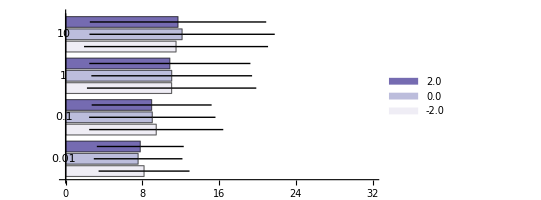

```mathematica
tipping2 = Table[Around[tipping[[i]][[j]][[1]][[1]],Sqrt[tipping[[i]][[j]][[2]][[1]]]], {i, {1, 2, 3,4}},{j,{1, 2, 3}}];
horizontal=BarChart[tipping2, BarOrigin->Left,
  FrameLabel -> Automatic, ChartLabels->{{"0.01","0.1","1", "10"},None}, ChartLegends->{"-2.0","0.0","2.0"}, ChartStyle->colors, PlotRange->{{0,32},All}, AspectRatio->1/2]
```